# Stylized Facts

## Initialization

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"],Orange,Purple,Brown};
```

### Package information

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

DatedTrendDuration[datedprices]
DatedTrendDuration[dates, prices]
calculates TrendDuration with date info.

## Database

```mathematica
path = FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Prices","DJI_NASDAQ_MXX_NIKKEI_datasetV2.wdx"}];
database = Import[path];
database[[All,"Name"]] = {"DJIA","NASDAQ Composite","IPC","Nikkei 225"};
```

Date fixer: There are no dates in the original dataset, this generates the intermediate dates.

```mathematica
GenerateDaysBetween[firstDate_DateObject,lastDate_DateObject,length_]:=Block[{dayRange,dayCount,ratio},
dayRange = DayRange[firstDate,lastDate];
dayCount = DayCount[firstDate,lastDate];
ratio = dayCount/length;
Table[Part[dayRange,Floor[i*ratio]],{i,length}]
];
AddToDataset[database,"Dates",GenerateDaysBetween[DateObject[#1],DateObject[#2],Length[#3]]&,{"FirstDate","LastDate","Prices"}];
```

```mathematica
djia = First[database];
```

```mathematica
ipc = database[[3]];
```

## Ausencia de autocorrelaciones

```mathematica
parts = Partition[Returns[ipc["Prices"]],2000];
datesPart = Map[#[[1000]]&,Partition[ipc["Dates"],2000]];
corr = Map[CorrelationFunction[#,{20}]&,parts];
```

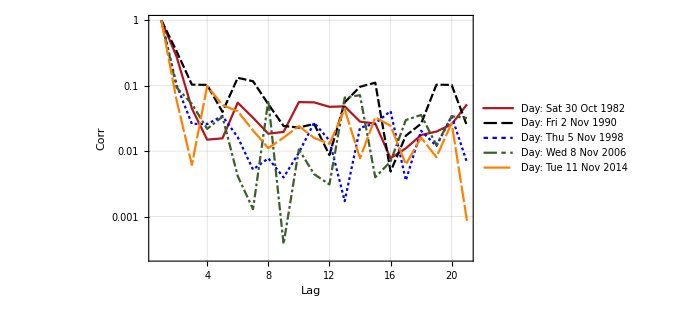

```mathematica
ListLinePlot[
Abs[corr],
PlotRange->All,
ScalingFunctions->"Log",
PlotLegends->datesPart,
ImageSize->500,
PlotTheme->"Monochrome",
FrameLabel->{Style["Lag",15],Style["Corr",15]},
Frame->True,BaseStyle->FontSize->14,
TicksStyle->Large,
PlotMarkers->None, 
PlotStyle->colors,
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Opacity[0.3]]
]
```

## Colas pesadas

```mathematica
HistogramPoints[data_]:=Transpose[MapAt[Drop[#,1]&,HistogramList[data,Automatic,"Count"],1]];
HistogramPointPlot[data_,opts: OptionsPattern[]]:=Block[{pltData = HistogramPoints[data]},
ListPlot[
pltData,
Joined->False,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{First[colors],{PointSize[Large],First[colors]}},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FilterRules[{opts},Options[ListPlot]]
]
];
```

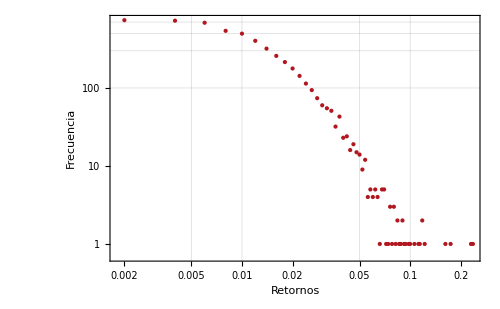

```mathematica
HistogramPointPlot[
Select[Returns[ipc["Prices"]],Positive],
PlotRange->All,
ScalingFunctions->{"Log","Log"},
FrameLabel->{Style["Retornos",15],Style["Frecuencia",15]}
]
```

## Asimetría ganancia-pérdida

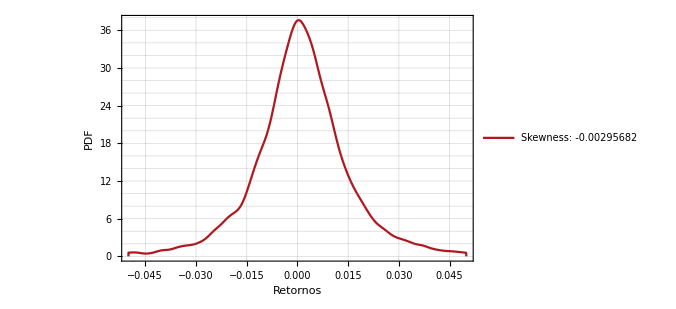

```mathematica
ret = Returns[ipc["Prices"]];
SmoothHistogram[
ret,
PlotRange->{{-0.05,0.05},All},
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->First[colors],
ImageSize->500,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->Placed[
LineLegend[{"Skewness: "<>ToString[Skewness[ret]]},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Top}
],
FrameLabel->{Style["Retornos",15],Style["PDF",15]}
]
```

## Agrupamiento de la volatilidad

```mathematica
parts = Partition[Returns[ipc["Prices"]]^2,2000];
datesPart = Map[#[[1000]]&,Partition[ipc["Dates"],2000]];
corr = Map[CorrelationFunction[#,{100}]&,parts];
```

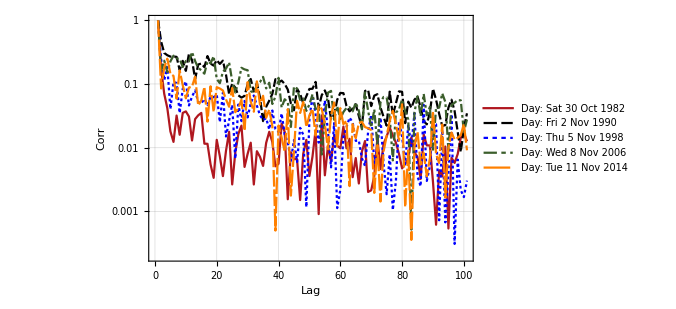

```mathematica
ListLinePlot[
Abs[corr],
PlotRange->All,
ScalingFunctions->"Log",
PlotLegends->datesPart,
ImageSize->500,
PlotTheme->"Monochrome",
FrameLabel->{Style["Lag",15],Style["Corr",15]},
Frame->True,BaseStyle->FontSize->14,
TicksStyle->Large,
PlotMarkers->None, 
PlotStyle->colors,
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Opacity[0.3]]
]
```